```mathematica
a =1.9058939019661396;L=1;v=0.5;
```

```mathematica
s=NDSolve[{x'[t]==Cos[(0.5*Pi/L)*(t*(v*Sin[a])-L)]+v*Cos[a],x[0]==0},{x},{t,50}];
```

```mathematica
p1=ParametricPlot[{x[t],-1+t vv  Sin[a]}/.s,{t,0,2*L/(v*Sin[a])},PlotRange->All,Axes->True,AxesLabel->{x,y},PlotStyle->Red];
```

```mathematica
vf=VectorPlot[{Cos[(0.5*Pi/L)*y],0},{x,0,2},{y,-L,L}];
```

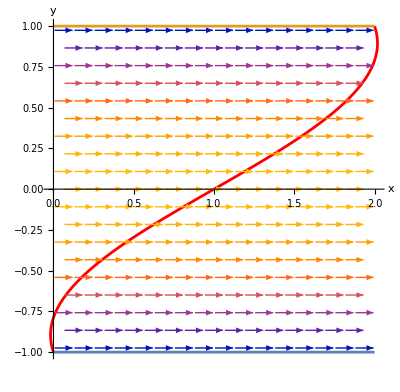

```mathematica
Show[{p1,vf,Plot[{-L,L},{x,0,2}]}]
```